# Finite Differencing: h≈0?

The idea behind Finite Difference approximations to derivatives is simple.  Since 
	f'(x)=lim_(h->0) (f(x+h)-f(x))/h
we should be able to choose h small and use the approximation 
	f'(x)≈(f(x+h)-f(x))/h.
There are lots of other possibilities
	f'(x)≈(f(x+h)-f(x-h))/(2h)
There are wider symmetric possibilities
	f'(x)≈(-f[x+2h]+8f[x+h] - 8f[x-h]+f[x-2h])/(12h)
and 
	f'(x)≈(f(x+3h)-9f(x+2h)+ 45 f(x+h)-45 f(x-h) + 9f(x-h)+f(x-3h))/(60h)
The question is how should we choose h small

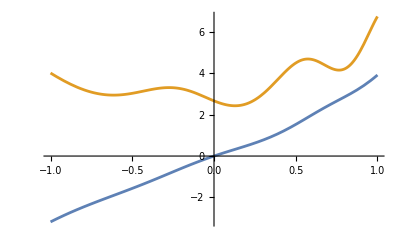

```mathematica
Clear[f]
f[x_]:= x Cos[Sin[x^2+ 3 x+1]+ Tan[x/2]]+2x +x^3
Plot[{f[x],f'[x]},{x,-1,1}]
```

You can compute the truncation error with series.

```mathematica
Clear[f,x0,h]
Series[ (f[x0+h]-f[x0])/h,{h,0, 1}]
Series[ (f[x0+h]-f[x0-h])/(2h),{h,0, 3}]
Series[(-f[x0+2h]+8f[x0+h] - 8f[x0-h]+f[x0-2h])/(12h),{h,0, 5}]
Series[(f[x0+3h]-9f[x0+2h]+ 45 f[x0+h]-45 f[x0-h] + 9f[x0-2h]-f[x0-3h])/(60h),{h,0,7}]
```

f'[x0]+1/2 f''[x0] h+O[h]^2

f'[x0]+1/6 f^(3)[x0] h^2+O[h]^4

f'[x0]-1/30 f^(5)[x0] h^4+O[h]^6

f'[x0]+1/140 f^(7)[x0] h^6+O[h]^8

The rounding error in each formula is ~ϵ_m/h.  The crude heuristic power for the optimal h is obtained by balancing these errors assuming that all the coefficients in the truncations and rounding are 1. 
	 ϵ_m/h_FD | ≈ | h_FD | ⇒ | h_FD | ≈ | ϵ_m^(1/2)
ϵ_m/h_CD_3 | ≈ | h_CD_3^2 | ⇒ | h_CD_3 | ≈ | ϵ_m^(1/3)
ϵ_m/h_CD_5 | ≈ | h_CD_5^4 | ⇒ | h_CD_5 | ≈ | ϵ_m^(1/5)
ϵ_m/h_CD_7 | ≈ | h_CD_7^6 | ⇒ | h_CD_7 | ≈ | ϵ_m^(1/7)

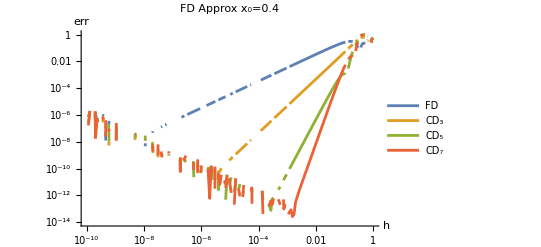

```mathematica
Clear[f]
f[x_]:= x Cos[Sin[x^2+ 3 x+1]]+2x +x^3
Plot[{f[x],f'[x]},{x,-1,1}];
x0=0.4;
eps=$MachineEpsilon;
Pic=LogLogPlot[ {
Abs[f'[x0] - (f[x0+h]-f[x0])/h],
Abs[f'[x0] - (f[x0+h]-f[x0-h])/(2h)],
Abs[f'[x0]-(-f[x0+2h]+8f[x0+h] - 8f[x0-h]+f[x0-2h])/(12h)],
Abs[f'[x0]-(f[x0+3h]-9f[x0+2h]+ 45 f[x0+h]-45 f[x0-h] + 9f[x0-2h]-f[x0-3h])/(60h)]
},
{h,10^-10,1},
MaxRecursion->2,
PlotRange->{10^-14,1},
GridLines->{{eps^(1/2),eps^(1/3),eps^(1/5),eps^(1/7)},Automatic},
PlotLabel->StringForm["FD Approx x_0=``",x0],
AxesLabel->{"h","err"},
PlotLegends->{"FD","CD_3","CD_5","CD_7"}]
```

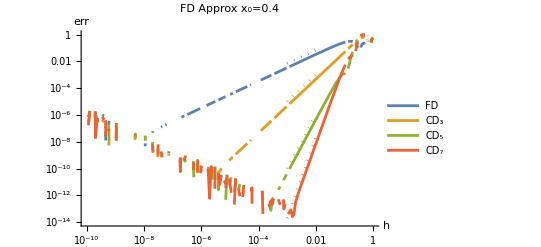

```mathematica
Show[Pic,
LogLogPlot[{7 h,10h^2,100h^4,2 10^4 h^6},{h, 0.001,0.01},PlotStyle->Dotted]
]
```

Our ODE precision target is not 10^-16.  It is a precision target of 10^-10 or something like it.